```mathematica
sp[f_]:=StreamPlot[f,{ϕ,-π,π},{θ,0,π},StreamColorFunction->None,StreamStyle->{Black, Thickness[.005]},StreamScale->None]
```

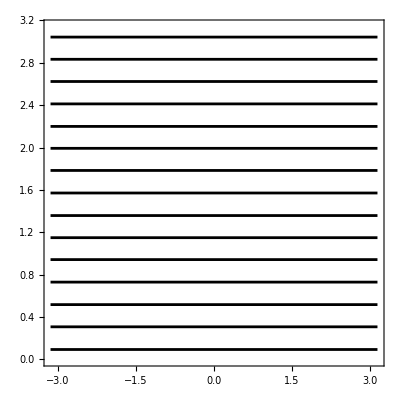

```mathematica
sp[{1,0}]
```

```mathematica
globe[f_]:=Graphics3D[{ReplaceAll[sp[f][[1]],{x_Real,y_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],Opacity[.8],Sphere[]},ImageSize->200, Boxed->False,Lighting->"Neutral",

ViewAngle->0.28746220718309295,ViewPoint->{1.507346866711427,-1.4563491683386212,2.6564925227251535},ViewVertical->{0.07694492783409525,0.38440548998095586,0.9199521168806054}]/.Arrow->Line
```

```mathematica
balls=Map[globe, {{1,0},{0,1},{1,1}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}